## Doppler Fitting

```mathematica
dataDoppler= Import["C:\\Users\\maruk\\Desktop\\Research\\PHY242\\retake\\EuropiumJ=9-2\\2022-06-08Pressure\\Pressure\\pressure\\DopplerR1.txt","Table"];
```

```mathematica
freq = dataDoppler[[All,1]]*4;
ydata = dataDoppler[[All,3]];
dataDopp = Transpose[{freq,ydata}];
ω0 =( -930.48987-3111 + 652384520);
m = 153*amu;
```

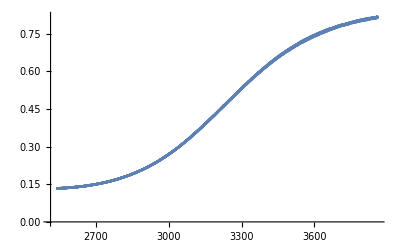

```mathematica
ListPlot[Transpose[{freq,ydata}]]
```

```mathematica
(*delt =535.478-930.48987;*)
Clear[delt]
model[x_] := offset -amp*Exp[-((x-x0)^2/(2( ω0 √(kb T/(m c^2)))^2))]-amp2*Exp[-((x-(x0-394))^2/(2( (ω0+394)√(kb T/(m c^2)))^2))]-amp3*Exp[-((x-x0-448.5)^2/(2( (ω0+448.5)√(kb T/(m c^2)))^2))];
```

```mathematica
params = {{offset,0.8},{amp,0.6},{x0,2600}, {T,500},(*{delt,394},*){amp2,.2},{amp3,.2}(*,{amp4,.2}*)(*,{delt2,448.5}*)};
```

```mathematica
nlm=NonlinearModelFit[dataDopp,model[f],params,f];
```

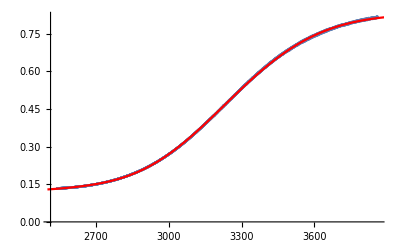

```mathematica
Show[ListPlot[dataDopp],Plot[nlm[f],{f,2500,3900}, PlotStyle->Red]]
```

```mathematica
nlm["BestFitParameters"]
```

{offset→0.829469,amp→0.245666,x0→2499.49,T→487.31,amp2→0.464951,amp3→0.454755}

```mathematica
2237.1-3200-165*4
```

-1622.9